```mathematica
$HistoryLength = 10;

findEvolutionOperator2D[Ham_]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8, 2}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8][[{1, 2, 3, 4, 5,6 , 7, 8}, {1, 2}]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]][[{1, 2}]]
)

fidelity2D[Mt_, Ma_] := (1/6)Sum[.25*Tr[Mt.(σI + σi).ConjugateTranspose[Mt].Ma.(σI + σi).ConjugateTranspose[Ma]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}];

Clear[fidelityToGate];
fidelityToGate[Ea_?NumericQ, Ba_?NumericQ, ωEin_?NumericQ, ωBin_?NumericQ, Tmaxin_?NumericQ,gate_] := (
HcorrectedAtStart = Hcorrected;

Clear[Eamp, Bamp, Eamp2, Bamp2, Eamp3, Bamp3];
Eamp[t_] := Ea*tanhWindow[t, Tmax, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax, Tmax]^2;
ωE = ωEin;
ωB = ωBin;
Tmax = Tmaxin;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];
U = (ConjugateTranspose[Ubase])[[{1, 2}, {1, 2}]].findEvolutionOperator2D[Hcorrected];
F = fidelity2D[gate, U /. t->Tmax] // Chop;

Print[{F, {ΔE, B0, Ea, Ba, ωEin, ωBin, Tmax}}];

output = F;

If[output > bestSoFar, (
bestSoFar = output;
bestParameters = {ΔE, B0, Ea, Ba, ωEin, ωBin, Tmax};
)];

Pause[2];

output
)


(* fidelityToY[EaD, BaD, ωED, ωBD] *)


setVariables[];
ΔE = -5000;
(* DEFAULTS *)
B0D = B0;
BaD =.0025;
ωED = 2*π*ϵ0;
ωBD = 2*π*(B0*γe);

Print["----------------------------------------" <> "startin'"<> "----------------------------------------"];
TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

NMaximize[
{
fidelityToGate[
0,
map[x1, BaD*.5, BaD*1.5],
ωED,
ωBD,
100*10^-9,
σZ],
0 < x1 < 1
},
{x1},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]

clearVariables[]
```

----------------------------------------startin'----------------------------------------

{0.6582,{-5000,0.2,0,0.00192072,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.604208,{-5000,0.2,0,0.0035717,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.456186,{-5000,0.2,0,0.00144186,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.99794,{-5000,0.2,0,0.00274621,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.604208,{-5000,0.2,0,0.0035717,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.872862,{-5000,0.2,0,0.00233347,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.902419,{-5000,0.2,0,0.00315896,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.982045,{-5000,0.2,0,0.00295259,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.956243,{-5000,0.2,0,0.00253984,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.997875,{-5000,0.2,0,0.0028494,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.983453,{-5000,0.2,0,0.00264303,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999819,{-5000,0.2,0,0.00279781,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.997875,{-5000,0.2,0,0.0028494,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999347,{-5000,0.2,0,0.00277201,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999334,{-5000,0.2,0,0.0028236,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999701,{-5000,0.2,0,0.00278491,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999697,{-5000,0.2,0,0.0028107,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.99979,{-5000,0.2,0,0.00279136,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999788,{-5000,0.2,0,0.00280425,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999812,{-5000,0.2,0,0.00279458,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999811,{-5000,0.2,0,0.00280103,1.19297×10^11,3.51481×10^10,1/10000000}}

{0.999817,{-5000,0.2,0,0.00279619,1.19297×10^11,3.51481×10^10,1/10000000}}

$Aborted

### Change driving strength to shift the Z-gate’s phase

3.13771

0.999813

(0.25585-0.966705 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.252054+0.967535 ⅈ)

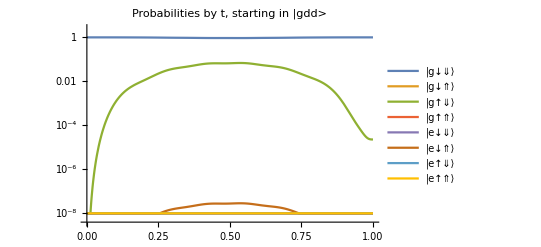

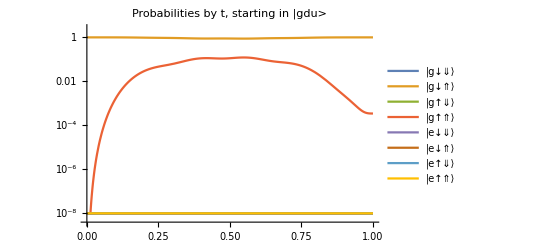

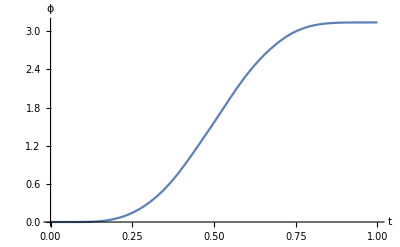

```mathematica
setVariables[]

Clear[angle];
angle[U_] := ArcTan[Re[U[[2, 2]]/U[[1, 1]]], Im[U[[2, 2]]/U[[1, 1]]]]

unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)

{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} ={-1000,0.2,0,0.0025084296125549863,4.2043831412317345*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,0.0026856682476131344,5.766889065694458*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-5000,0.2,0,0.0027961930043725533,1.192971972765056*^11,3.51481386083626*^10,1/10000000};
ωE = (ωE + ωB)/2;

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax, Tmax]^2;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];

Uax = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected];
U = Uax/. t->Tmax;
targetGate = {{1, 0}, {0, -1}};
angle[U]
F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop
U[[{1, 2}, {1, 2}]] // MatrixForm

Evaluate@Table[Max[Abs[Uax[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uax[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]
Plot[angle[Uax], {t, 0, Tmax}, AxesLabel->{"t", "ϕ"}]

(*(* Loop through different values of ξ *)
ϕs = {};
ξs = Table[i*.1, {i, 0, 20}];

Do[
Clear[Bamp];
Bamp[t_] := ξ*Ba*tanhWindow[t, Tmax, Tmax]^2;

Uax = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected];
U = Uax/. t->Tmax;

targetGate = {{1, 0}, {0, E^(ⅈ*angle[U])}};
F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop;

(*U // MatrixForm
targetGate // MatrixForm*)

Print[ {ξ, angle[U], F}];
AppendTo[ϕs, {ξ, angle[U], F}];

,{ξ, ξs}]

ϕs[[All, 2]] = unravel[ϕs[[All, 2]]];
ϕFunction = Interpolation[ϕs[[All, {1, 2}]]];

Clear[ξ]
Plot[ϕFunction[ξ], {ξ, 0, 1}, AxesLabel->{"ξ", "ϕ"}]*)


clearVariables[]
```

```mathematica
(* Plot results *)

ϕs[[All, 2]] = unravel[ϕs[[All, 2]]];
ϕFunction = Interpolation[ϕs[[All, {1, 2}]]];
FFunction = Interpolation[ϕs[[All, {1, 3}]]];

setVariables[]
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} ={-1000,0.2,0,0.0025084296125549863,4.2043831412317345*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,0.0026856682476131344,5.766889065694458*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-5000,0.2,0,0.0027961930043725533,1.192971972765056*^11,3.51481386083626*^10,1/10000000};

ωE = (ωE + ωB)/2;
Eamp[t_] := Ea*tanhWindow[t, Tmax, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax, Tmax]^2;

integral = NIntegrate[tanhWindow[t, Tmax, Tmax]^4, {t, 0, Tmax}];
ϕAnalytical[ξ_] := 2*((π/2)*ξ*Ba*γe)^2/(2*π*A*dState[[1]]^2/2)*integral
ϕAnalytical[ξ_] := 2*NIntegrate[
-(2*π*A*dState[[1]]^2/4)
 + Sqrt[(2*π*A*dState[[1]]^2/4)^2 + ((π/2)*ξ*Ba*γe*tanhWindow[t, Tmax, Tmax]^2)^2]
, {t, 0, Tmax}]

Clear[ξ]
ParametricPlot[{
{ξ*Ba*1000, ϕFunction[ξ]},
{ξ*Ba*1000, ϕAnalytical[ξ]}
}, {ξ, 0, 1.5}, AxesLabel->{"B_max (mT)", "ϕ"}, PlotStyle->{Blue, Dashed}, PlotLegends->{"True phase","Approximation"}, AspectRatio->.6]
LogPlot[1 - FFunction[B/Ba/1000], {B, 0, 1.5*Ba*1000}, AxesLabel->{"B_max (mT)", "1 - F"}, PlotRange->{10^-6, 10^-3}]

clearVariables[]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::noval: Symbol ϕs in part assignment does not have an immediate value.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Interpolation::innd: First argument in Symbol[] does not contain a list of data and coordinates.

$Aborted

$Aborted

## Look at the effect of noise on a Z-gate

F from approximation: 0.999813

F exact: 0.999777

{-5600,0.999761}

{-5580,0.999763}

{-5560,0.999766}

{-5540,0.999768}

{-5520,0.99977}

{-5500,0.999772}

{-5480,0.999774}

{-5460,0.999776}

{-5440,0.999778}

{-5420,0.99978}

{-5400,0.999783}

{-5380,0.999785}

{-5360,0.999786}

{-5340,0.999788}

{-5320,0.99979}

{-5300,0.999792}

{-5280,0.999794}

{-5260,0.999796}

{-5240,0.999798}

{-5220,0.9998}

{-5200,0.999801}

{-5180,0.999803}

{-5160,0.999804}

{-5140,0.999805}

{-5120,0.999807}

{-5100,0.999809}

{-5080,0.999809}

{-5060,0.999811}

{-5040,0.999813}

{-5020,0.999814}

{-5000,0.999815}

{-4980,0.999817}

{-4960,0.999818}

{-4940,0.999819}

{-4920,0.99982}

{-4900,0.99982}

{-4880,0.99982}

{-4860,0.999821}

{-4840,0.999822}

{-4820,0.999823}

{-4800,0.999824}

{-4780,0.999824}

{-4760,0.999824}

{-4740,0.999825}

{-4720,0.999825}

{-4700,0.999825}

{-4680,0.999825}

{-4660,0.999824}

{-4640,0.999824}

{-4620,0.999824}

{-4600,0.999823}

{-4580,0.999823}

{-4560,0.999822}

{-4540,0.999821}

{-4520,0.99982}

{-4500,0.999819}

{-4480,0.999818}

{-4460,0.999817}

{-4440,0.999816}

{-4420,0.999814}

{-4400,0.999812}

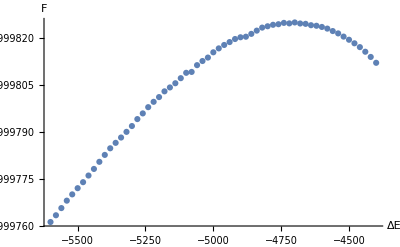

```mathematica
setVariables[]

{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-2000,0.2,0,0.0026856682476131344,5.766889065694458*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-1000,0.2,0,0.0025084296125549863,4.2043831412317345*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-500,0.2,0,0.002348976959331582,3.71238395425843*^10,3.51481386083626*^10,1/10000000};
{ΔE, B0, Ea, Ba, ωE, ωB, Tmax} = {-5000,0.2,0,0.0027961930043725533,1.192971972765056*^11,3.51481386083626*^10,1/10000000};
ωE = (ωE + ωB)/2;

Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax, Tmax]^2;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];
UbaseLab = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HexactStatic]]];

Uax = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected];
F = fidelity2D[targetGate, Uax[[{1, 2}, {1, 2}]] /. t->Tmax] // Chop;
Print["F from approximation: " <> ToString[F]]
Uex = ConjugateTranspose[UbaseLab].findEvolutionOperator[Hexact];
F = fidelity2D[targetGate, Uex[[{1, 2}, {1, 2}]] /. t->Tmax] // Chop;
Print["F exact: " <> ToString[F]]

Fs = {};
ΔEs = Table[e + ΔE, {e, -600, 600, 20}];

Do[
(
ΔE = deltaE;
Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];
Uax = (ConjugateTranspose[Ubase])[[{1, 2}, {1, 2}]].findEvolutionOperator2D[Hcorrected];
(*Uex = findEvolutionOperator[Hexact];*)
(*M = ConjugateTranspose[Uex].Uax;*)

(*Plot[fidelity[M], {t, 0, Tmax}, PlotLabel->"Fidelity of Approximation to True Evolution"]*)

U = Uax/. t->Tmax;

F = fidelity2D[targetGate, U] // Chop;

AppendTo[Fs, {ΔE, F}];

Pause[.5];

Print[{ΔE, F}];
),

{deltaE, ΔEs}
]

clearVariables[]

ListPlot[Fs, AxesLabel->{"ΔE", "F"}]
```

```mathematica
FsZ = Fs;
```

{0.00377279,0.00156026,0.000228022,0.000185613}

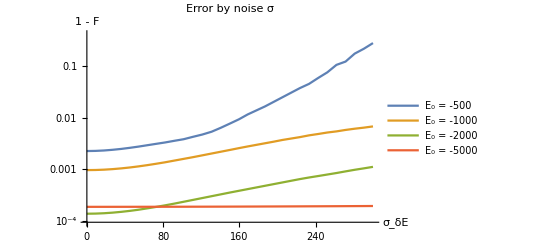

```mathematica
Clear[FgivenSD]
FgivenSD[σ_?NumericQ, μ_, Fint_] := (
Mean[Fint[RandomVariate[NormalDistribution[μ, σ], 100000]]]
)

fidelityData = {{FsZn500, -500, "E_0 = -500"}, {FsZn1000, -1000, "E_0 = -1000"}, {FsZn2000, -2000, "E_0 = -2000"}, {FsZn5000, -5000, "E_0 = -5000"}} // Transpose;

fidelityPoints = fidelityData[[1]];
means = fidelityData[[2]];
names = fidelityData[[3]];

Fints = Map[Interpolation, fidelityPoints];

Evaluate@Table[1 - FgivenSD[σ, means[[i]], Fints[[i]]], {i, Length[names]}] /. σ->100

LogPlot[Evaluate@Table[1 - FgivenSD[σ, means[[i]], Fints[[i]]], {i, Length[names]}], {σ, .0001, 300}, AxesLabel->{Subscript[σ, δE], "1 - F"}, PlotLegends->names, PlotLabel->"Error by noise σ", PlotPoints->5, MaxRecursion->3]
```